# Caso 2: Modelado de protocolos ARQ para análisis de rendimiento

```mathematica
Clear["Global`*"];
```

```mathematica
<<"/home/david/Documentos/RRT/RandomData.m"
<<"/home/david/Documentos/RRT/drawTx.m"
```

```mathematica
?drawTx`*
```

Apartado 1
Estudiar librería de representación de paquetes y averiguar el formato del paquete
mu=C/l donde mu es en paq/s, l es bits/paquete y C es bits/segundo
DrawWin: para dibujar una ventana temporal 
DrawPacket: para dibujar los paquetes
SetIniParDraw[prop_time,ack_time]: configura parámetros de transmisión
Paquete = {tiempo_llegada, tasa_servicio*9600, num_sec, error, num_rep} la tasa de servicio 9600 equivale a un segundo (por defecto) y es el tamaño del paquete

Apartado 2
Probar la representación de la librería para un caso particular de Stop & Wait sin errores y con tiempo de propagación 0. Posteriormente hacerlo proporcionando otros valores a cada parámetro

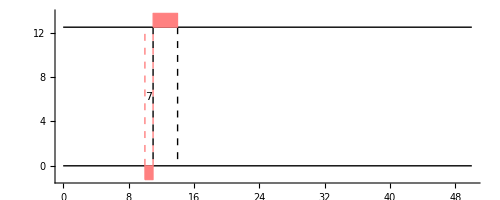

```mathematica
SetIniParDraw[0,3];
GetIniParDraw[];
packet={10,9600,7,0,0};
Show[DrawWin[0,50,10],DrawPacketTx[packet]]
```

```mathematica
(*pktLength+prop_time*2+ack_time=tiempo_llegada --> para que sea Stop&Wait*)
SetIniParDraw[2,2]
pktLength=4;
packets=Table[{n*10,pktLength *9600,n,0,0},{n,0,9}];
Manipulate[Show[DrawWin[0,width,5],Map[DrawPacketTx[#]&,packets]],{width,10,200}]
```

Apartado 3
Cola MM1

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
Map[
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&,
arrivals]]
```

```mathematica
(*Con esto se calcula el tiempo que espera cada paquete en la cola antes de entrar en el enlace (desde que llega hasta que se sirve)*)
InsertionTime[departures_, service_]:=
Module[{i=0,insertionTime={}},
For[i=0,i<Length[departures],i++,
AppendTo[insertionTime,departures[[i]]-service[[i]]
]
];
Return[insertionTime]
]
```

```mathematica
lambda=70;mu=100;pktNumber=100;
InterArrivalsTime=Table[RandomExp[lambda],pktNumber];
ArrivalsTime=Accumulate[InterArrivalsTime];
ServiceTime=Table[RandomExp[mu],pktNumber];
Departures=FifoSchedulling[ArrivalsTime,ServiceTime];
insertionTime=InsertionTime[Departures,ServiceTime];
```

```mathematica
packetsMM1Func[inserTime_,servTime_ ]:=
Module[{i,packets={}},
For[i=0,i<Length[inserTime],i++,AppendTo[packets,{inserTime[[i]],servTime[[i]]*9600,i,0,0}]
];
Return[packets]
]
```

```mathematica
packetsMM1=packetsMM1Func[insertionTime,ServiceTime];
```

```mathematica
propTime=0.05;ackTime=0.004;
SetIniParDraw[propTime,ackTime];
```

```mathematica
Manipulate[Show[DrawWin[0,width,10],Map[DrawPacketTx[#]&,packetsMM1]],{width,0,1}]
```

```mathematica
ArrivalsTime[[1;;10]]
```

{0.0014741,0.074636,0.116521,0.148878,0.162355,0.167548,0.227213,0.574302,0.649828,0.691782}

```mathematica
ServiceTime[[1;;10]]
```

{0.0281981,0.00315505,0.0333245,0.0145864,0.0664106,0.000508607,0.00427929,0.00496451,0.00470153,0.083628}

```mathematica
Departures[[1;;10]]
```

{0.0296723,0.077791,0.149846,0.164432,0.230843,0.231351,0.235631,0.579267,0.65453,0.77541}

```mathematica
insertionTime[[1;;10]]
```

{0,0.00814929,0.0113585,0.0342902,0.0549974,0.0614262,0.0726225,0.0880371,0.108816,0.119534}

### Protocolo Stop&Wait

### Protocolo GoBackN